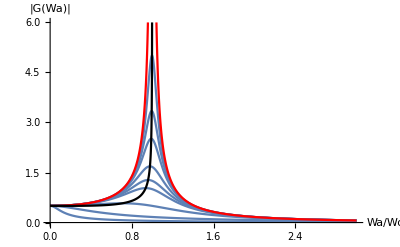

```mathematica
w0=1;
Show[Table[Plot[0.5/Sqrt[1*((w^2-w0^2))^2+i^2*w^2],{w,0,3},PlotRange->Full],{i,{i,0.1,0.15,0.2,0.3,0.4,0.5,1,3,10}}],Plot[0.5/Abs[1-(w/w0)^2],{w,0,3},PlotRange->{{0,3},{0,6}},PlotStyle->{Red}],Plot[0.5/Sqrt[1-(w/w0)^4],{w,0,3},PlotRange->{{0,3},{0,6}},PlotStyle->{Black}],PlotRange->All,AxesLabel->{"Wa/Wo","|G(Wa)|"}]
```

```mathematica
Manipulate[s=NDSolve[{m*D[x'[t],t]+b*x'[t]+c*x[t]^2==A*Cos[w*t],x[0]==x0,x'[0]==v0},x[t],{t,0,3}];
ParametricPlot[{t,x[t]}/. s,{t,0,3}],{m,1,10},{b,1,10},{c,1,10},{w,1,10},{A,1,10},{v0,1,10},{x0,1,10}]
```

```mathematica
Manipulate[s=NDSolve[{m*D[x'[t],t]+b*x'[t]+c*x[t]^2==A*Cos[w*t],x[0]==x0,x'[0]==v0},x[t],{t,0,3}],{m,1,10},{b,1,10},{c,1,5},{w,1,10},{A,1,10},{v0,1,10},{x0,1,10}]
```

```mathematica
Manipulate[s=DSolve[{m*D[x'[t],t]+b*x'[t]+c*(x[t])^2==A*Cos[w*t],x[0]==x0,x'[0]==v0},x[t],t],{m,1,10},{b,1,10},{c,0,5},{w,1,10},{A,1,10},{v0,1,10},{x0,1,10}]
```

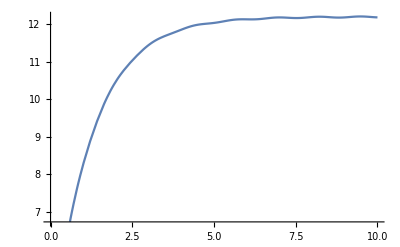

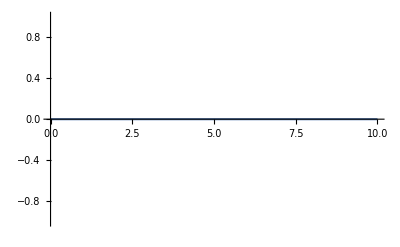

```mathematica
Plot[-0.01362567957993263 ⅇ^(-0.8183962264150945 t) (653.6377869740634-895.3597253374649 ⅇ^(0.8183962264150945 t)+1. ⅇ^(0.8183962264150945 t) Cos[4.96 t]-0.16499923919659168 ⅇ^(0.8183962264150945 t) Sin[4.96 t]),{t,0,10}]
```